```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
<<MaTeX`;
sf=1.17;
```

```mathematica
getAssoc[head_,JRange_,tail_]:=(
result={};
Do[(
file=StringJoin[head,"_1.0_",J,"_",tail,".json"];
sData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,sData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
interactionAvail=Normal[DeleteDuplicates[ds[Take,"interaction"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
hoppingAvail=Normal[DeleteDuplicates[ds[Take,"hopping"]]];
<|"size"->sizeAvail,"interaction"->interactionAvail,"coupling" ->couplingAvail, "hopping"->hoppingAvail|>
)
```

```mathematica
extractData[ds_,directive_,keys_,n_]:=(
data=Apply[ds,directive];
{x,y}=Table[(data[Take,keys[[i]]]//Normal)[[1]],{i,1,2}];

Return[Table[{x[[i]],y[[i]]/y[[sizeAvail[[1]]]]},{i,Length[x]}]]
)
```

```mathematica
StandardNumberForm[x_]:=If[FractionalPart[x]==0,IntegerPart[x],x];
tlf=(MaTeX[ToString[StandardNumberForm[#]]]&);
```

```mathematica
getDPlot[spc_,n_]:=(
SetOptions[MaTeX,Magnification->1.6sf];

fs=22;
tckn=0.005;

If[B==1.,inplt=ListPlot[spc,
SetOptions[LinTicks,TickLengthScale->2.5];
ImageSize->240,
Joined->False,
PlotMarkers->{"●",10},
PlotStyle->If[B==1.,Orange,Purple],
Frame->True,Axes->False,
PlotRangeClipping->True,
ClippingStyle->Automatic,
FrameStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
FrameTicksStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
LabelStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
FrameLabel->MaTeX@{"n","c_n/c_0"},
PlotRange->{{0,n-1},{0.75,1.05}},
AspectRatio->0.75,
PlotLegends->Placed[PointLegend[{Orange},{MaTeX["\\lambda = 1"]},LegendMarkerSize->12],{0.64,0.85}],
FrameTicks->{{LinTicks[0.5,1.5,0.1,2,TickLabelFunction->tlf],LinTicks[0.5,1.5,0.1,2,ShowTickLabels->False]},{LinTicks[-30,30,10,10,TickLabelFunction->tlf],LinTicks[-30,30,10,10,ShowTickLabels->False]}},
Epilog->{
Inset[MaTeX["\\text{(b) }"],Scaled[{0.2,0.8}]],
Inset[MaTeX["(t\\text{--}J)"],Scaled[{0.71,0.67}]]
}
]];

plt=ListPlot[spc,
SetOptions[LinTicks,TickLengthScale->1.5];
ImageSize->360,
Joined->False,
PlotMarkers->If[B==1,
{"●",10},
If[B==0.0,
{"■",13},
If[B==0.99,
{"◆",12},
If[B==0.5,
{"▼",12},
{"▲",12}
]]]],
(*Mesh->15,*)
PlotStyle->If[B==1.,
Orange,
If[B==0.0,
Purple,
If[B==0.99,
Lighter[Blend[{Orange,Red},0.75]],
If[B==0.5,
Lighter[Blend[{Red,Purple},0.75]],
Lighter[Blend[{Red,Purple},0.25]]
]
]]],(*{Opacity[0.5,Blue]}*)
Frame->True,Axes->False,
FrameStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
LabelStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
(*InterpolationOrder->0,*)
PlotRange->{{0,n-1},{10^-17,9.9}},
PlotRangeClipping->True,
(*PlotLegends->Placed[Automatic,Right],*)
ClippingStyle->Automatic,
AspectRatio->0.85,
FrameLabel->MaTeX@{"n","-\\log_{10}(c_n / c_0)"},
Epilog->
Join[{
(*Inset[
MaTeX["\\text{(a) }"],
{3,-10}]*)
},
If[(*B==1.*)False,{
Inset[inplt,{4.5,-24},{1,1},13],
Text[Style["n",Black,fs,FontFamily->"CMU Serif"],{9.5,-37.5}],
Rotate[Text[Style["c_n / c_n",Black,fs,FontFamily->"CMU Serif"],{1.35,-28.25}],90Degree]
},{}]],
ScalingFunctions->"Log",
FrameTicks->{{Table[{10^-l,If[Mod[l,2]==0,MaTeX[l],""]},{l,-10,20,1}],Table[{10^-l,""},{l,-10,20,1}]},{LinTicks[-30,30,10,10,TickLabelFunction->tlf],LinTicks[-30,30,10,10,ShowTickLabels->False]}}
(*{LinTicks[-n+1,n+1,1,0],LogTicks[10,-5, 0],LinTicks[-n+1,n+1,1,0,ShowTickLabels->False],LogTicks[10,-5,0,ShowTickLabels->False]}*)
];

plt
)
```

```mathematica
makePlotsSpc[]:=(
dirc={Select[#coupling==J&&#size==n&&#interaction==B&]};
keys={"magnons","coefficients"};

plots={};
Do[(
Do[(
buff={};
Do[(
spc=extractData[spcDataset,dirc,keys,n];
AppendTo[buff,getDPlot[spc,n]];
),{B,spcAvail["interaction"]//Normal}];
AppendTo[plots,buff];
),{n,spcAvail["size"]//Normal}];
),{J,spcAvail["coupling"]//Normal}];

plots
)
```

```mathematica
JRange={"0.4"};
tails={"28-2-28_0.0-1.0-1.0","28-2-28_0.5-0.4-0.9","28-2-28_0.99-0.01-0.99"};
head = "mc";
spcPlots={};
Do[(
spcDataset=Dataset[getAssoc[head,JRange,tail]];
spcAvail=Dataset[getStruct[spcDataset]];
AppendTo[spcPlots,makePlotsSpc[]];
),{tail,tails}]
```

```mathematica
spcAvail
```

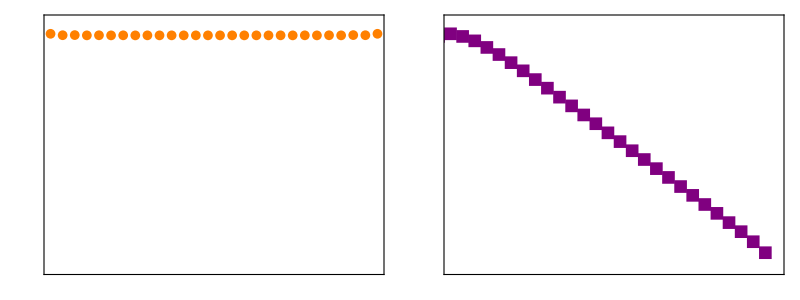

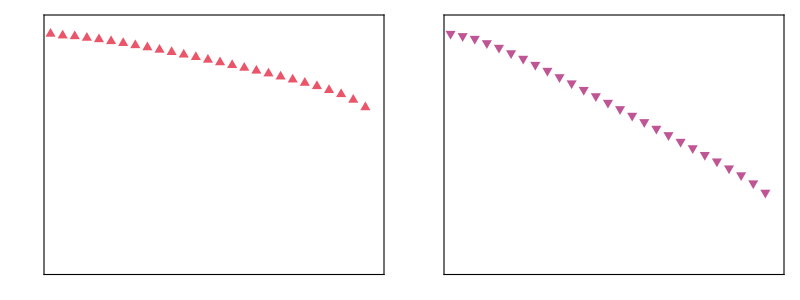

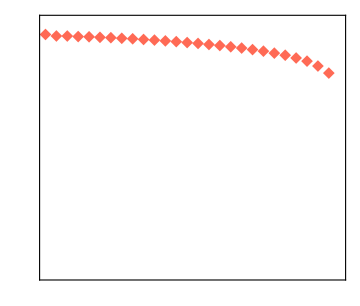

```mathematica
Grid[Reverse[spcPlots[[1]],2]]
Grid[Reverse[spcPlots[[2]],2]]
Grid[Reverse[spcPlots[[3]],2]]
```

```mathematica
SavePlots[]:=(
Do[(
Do[(
Do[(
fileName=StringJoin["plots/",head<>"r","/",
head<>"r","_L=",ToString[spcAvail["size"][[iN]]],
"_J=",ToString[spcAvail["coupling"][[iJ]]],
"_B=",ToString[spcAvail["interaction"][[iB]]],
".jpg"];
Export[fileName,spcPlots[[iN,iJ,iB]],ImageResolution->300];
),{iB,Length[spcAvail["interaction"]//Normal]}]
),{iJ,Length[spcAvail["coupling"]//Normal]}]
),{iN,Length[spcAvail["size"]//Normal]}]
)
```

```mathematica
(*SavePlots[]*)
```

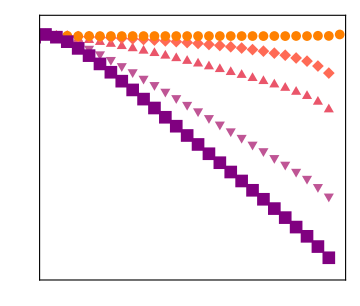

```mathematica
fs=22;
SetOptions[MaTeX,Magnification->1.75sf];
pltjoint=Legended[Show[spcPlots[[2,1]],Reverse[spcPlots[[3,1]]],Reverse[spcPlots[[1,1]]]],
Placed[PointLegend[Reverse[{Orange,Lighter[Blend[{Orange,Red},0.75]],Lighter[Blend[{Red,Purple},0.25]],Lighter[Blend[{Red,Purple},0.75]],Purple}],
MaTeX@Reverse[{"\\lambda = 1.0~(t\\text{--}J)","\\lambda = 0.99","\\lambda = 0.9","\\lambda = 0.5","\\lambda = 0.0"}],
LegendMarkerSize->16,Spacings->-0.25,
LegendMarkers->Reverse[{{"●",10},{"◆",12},{"▲",12},{"▼",12},{"■",13}}]],
{0.3,0.33}]
]
```

```mathematica
Export["plots/cns.png",pltjoint,ImageResolution->300]
```

plots/cns.png